Inverse::luc: Result for Inverse of badly conditioned matrix {{18.7279,13.8018,14.4701,14.5152,15.2991,14.2532,«39»,16.6658,14.1572,13.0965,14.5434,16.2417,«50»},«49»,«50»} may contain significant numerical errors.

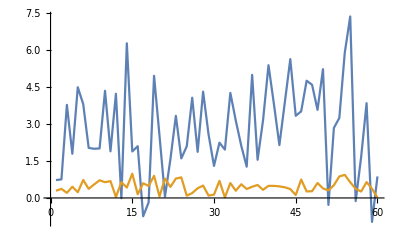

```mathematica
A=Table[RandomReal[{0,1}],{i,1,60},{j,1,100}];
b=Table[RandomReal[{0,1}],{i,1,60}];
x=Inverse[Transpose[A].A].Transpose[A].b;
ListPlot[{A.x,b},Joined->True]
```

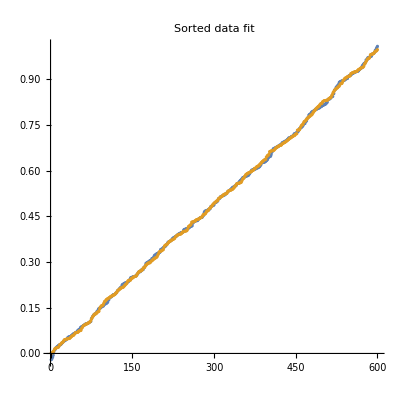

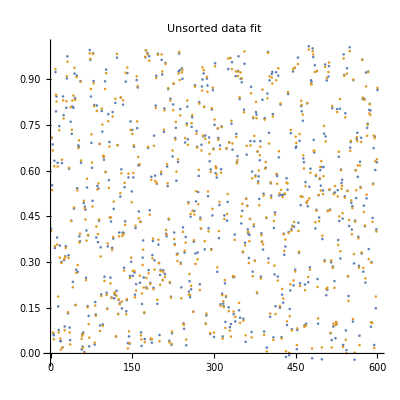

```mathematica
A=Table[RandomReal[{0,1}],{i,1,600},{j,1,600}];
b=Table[RandomReal[{0,1}],{i,1,600}];
Do[{
{U1,S1,V1}=SingularValueDecomposition[A],
{U,S,V}=SingularValueDecomposition[A,i],
x=V.Inverse[S].Transpose[U].b,
Subscript[p, i]=ListPlot[{Sort[A.x],Sort[b]},PlotLabel->"Sorted data fit",AspectRatio->1,PlotRange->{{0,600},{0,1}}],
Subscript[p2, i]=ListPlot[{A.x,b},PlotLabel->"Unsorted data fit",AspectRatio->1,PlotRange->{{0,600},{0,1}}]},{i,1,599}]
gif=Table[Subscript[p2, t],{t,1,599}];
Export["E:\\test_gif(4).gif",gif];
SystemOpen["E:\\test_gif(4).gif"];
gif=Table[Subscript[p, t],{t,1,599}];
Export["E:\\test_gif(5).gif",gif];
SystemOpen["E:\\test_gif(5).gif"];
ListPlot[{Sort[A.x],Sort[b]},PlotLabel->"Sorted data fit",AspectRatio->1]
ListPlot[{A.x,b},PlotLabel->"Unsorted data fit",AspectRatio->1]
```

```mathematica
StandardDeviation[A.x-b]
```

0.00988374